```mathematica
x = 2.1
Integrate[(y(x-y)-1)/(Sqrt[y^2-1]*Sqrt[(x-y)^2-1]),{y, 1, x-1}]
```

2.1

∫_1^1.1 (-1+(2.1-y) y)/(√(-1+(2.1-y)^2) √(-1+y^2))ⅆy

```mathematica
Simplify[∫_1^1.1 (-1+(2.1-y) y)/(√(-1+(2.1-y)^2) √(-1+y^2))ⅆy]
```

∫_1^1.1 (-1.+2.1 y-1. y^2)/(√(-1+y^2) √(3.41-4.2 y+y^2))ⅆy

```mathematica
N[-2 ⅈ √5 EllipticE[-4/5]-3 EllipticE[5/9]+2 √5 EllipticE[9/5]+(18 ⅈ EllipticK[-4/5])/(√5)-4/3 ⅈ EllipticK[4/9]+(4 EllipticK[9/5])/(√5)]
```

1.42737+1.77636×10^-15 ⅈ

```mathematica
N[-2 ⅈ √5 EllipticE[-4/5]-3 EllipticE[5/9]+(2 (5 EllipticE[9/5]+9 ⅈ EllipticK[-4/5]+4 EllipticK[9/5]))/(√5)]
```

3.96636+1.77636×10^-15 ⅈ

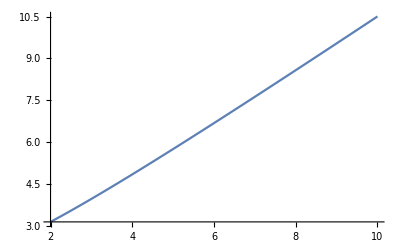

```mathematica
Plot[NIntegrate[(y(x-y)+1)/(Sqrt[y^2-1]*Sqrt[(x-y)^2-1]),{y, 1, x-1}], {x, 2,10}]
```

```mathematica
dat = Table[{x, Sin[x], Cos[x]},{x, 2, 10, 0.1}] // N;
Export["test_mathematica.txt",dat,"Table","FieldSeparators"->" "]

FilePrint["test.txt"]
```

test_mathematica.txt

2. 0.9092974268256817 -0.4161468365471424
3. 0.1411200080598672 -0.9899924966004454
4. -0.7568024953079282 -0.6536436208636119
5. -0.9589242746631385 0.28366218546322625
6. -0.27941549819892586 0.960170286650366
7. 0.6569865987187891 0.7539022543433046
8. 0.9893582466233818 -0.14550003380861354
9. 0.4121184852417566 -0.9111302618846769
10. -0.5440211108893698 -0.8390715290764524

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["test_mathematica.txt"]]]
```

```mathematica
S_minus[x_, y_]:=x+y
```

```mathematica
S_minus[2,2]
```

```mathematica
S_minus[2,2]
dat = Table[{x, NIntegrate[(y(x-y)-1)/(Sqrt[y^2-1]*Sqrt[(x-y)^2-1]),{y, 1, x-1}],  NIntegrate[(y(x-y)+1)/(Sqrt[y^2-1]*Sqrt[(x-y)^2-1]),{y, 1, x-1}]},{x, 2, 16, 0.01}] // N;
Export["S_minusplus.txt",dat,"Table","FieldSeparators"->" "]

FilePrint["S_minusplus.txt"]
```

S_minus[2,2]

S_minusplus.txt

2. 0. 0.
2.01 0.015688400289126908 3.149451257247075
2.02 0.03133796813740181 3.1573198505996873
2.03 0.04694913557839209 3.1651981535665685
2.04 0.06252232708686616 3.173086051969078
2.05 0.07805796054586137 3.1809834656485236
2.06 0.09355644826914683 3.188890351303976
2.07 0.10901819537142426 3.1968066253174254
2.08 0.12444360078882483 3.204732212123159
2.09 0.1398330676202667 3.2126672774434093
2.1 0.15518696555320027 3.2206113215425725
2.11 0.17050568355862525 3.228564478089018
2.12 0.18578959781131898 3.236526692232011
2.13 0.20103907777575036 3.244497888539905
2.14 0.21625448849452195 3.2524780115148966
2.15 0.23143618883382266 3.260466992857913
2.16 0.24658453232592387 3.2684647654020207
2.17 0.26169986813782203 3.276471274027446
2.18 0.27678253952638326 3.2844864528119984
2.19 0.29183288475082714 3.292510237226288
2.2 0.3068512379752272 3.30054257282751
2.21 0.3218379277399228 3.3085833961367266
2.22 0.33679327786310115 3.3166326448312486
2.23 0.3517176083177348 3.324690265269058
2.24 0.3666112337618428 3.3327561964438512
2.25 0.3814744520582109 3.340830267338566
2.26 0.3963075936494561 3.3489126442860693
2.27 0.41111094842574464 3.3570031599152195
2.2800000000000002 0.4258848136365383 3.3651017558632157
2.29 0.4406294831747142 3.3732083808452007
2.3 0.4553452460623902 3.381322977509572
2.31 0.47003238732127484 3.3894454893095505
2.32 0.4846911888160979 3.3975758660511497
2.33 0.49932192753916843 3.4057140505154955
2.34 0.5139248776977784 3.413859993308849
2.35 0.528500309000701 3.4220136400015924
2.36 0.5430484874971152 3.430174936855126
2.37 0.5575696764195304 3.4383438357791922
2.38 0.5720641346854254 3.446520283973373
2.39 0.5865321177410475 3.4547042292826053
2.4 0.6009738783946944 3.462895624810694
2.41 0.6153896653114644 3.471094419232511
2.42 0.6297797124696419 3.479300496194977
2.43 0.6441442852452883 3.4875139407157882
2.44 0.6584836115476362 3.495734638091956
2.45 0.6727979272035813 3.5039625391263813
2.46 0.6870874657271115 3.5121975992580188
2.47 0.7013524568390821 3.5204397701408556
2.48 0.7155931272850689 3.5286890039624113
2.49 0.7298097016482981 3.5369452573070084
2.5 0.7440024008688075 3.5452084831828112
2.51 0.7581714430471153 3.5534786350545886
2.52 0.7723170442937071 3.5617556707246365
2.5300000000000002 0.786439417186468 3.570039544450587
2.54 0.8005387716249817 3.5783302110405297
2.55 0.814615315610433 3.5866276292484964
2.56 0.828669253536617 3.5949317535107927
2.5700000000000003 0.8427007882326781 3.603242543286898
2.58 0.8567101085447482 3.61155990731734
2.59 0.8706974327135282 3.619883897221141
2.6 0.8846629456498587 3.6282144262948837
2.61 0.8986068396083017 3.6365514522082507
2.62 0.9125293044427583 3.644894932897995
2.63 0.9264305284307857 3.6532448298537363
2.64 0.9403106968185744 3.6616011017698247
2.65 0.9541699925990956 3.6699637077525695
2.66 0.9680085972801298 3.6783326102650316
2.67 0.9818266894484426 3.6867077690936196
2.68 0.9956244455410475 3.695089144418108
2.69 1.0094020405955324 3.7034766995994692
2.7 1.0231596468694963 3.711870395573169
2.71 1.0368974345318973 3.7202701935072646
2.7199999999999998 1.0506155724688804 3.728676057728387
2.73 1.0643142268484478 3.737087950091558
2.74 1.0779935618780825 3.745505832809365
2.75 1.0916537301498719 3.75392963293563
2.76 1.105294912669255 3.762359389320241
2.77 1.1189172577180813 3.7707950272977815
2.7800000000000002 1.1325209226623303 3.779236512909786
2.79 1.1461060621280046 3.7876838091800282
2.8 1.1596728298706673 3.7961368827096127
2.81 1.1732213771774505 3.8045956978922235
2.8200000000000003 1.186751853599224 3.813060219448707
2.83 1.200264407687243 3.8215304148461575
2.84 1.213759185593157 3.830006249372534
2.85 1.2272363318071633 3.8384876886287316
2.86 1.2406959898915098 3.8469747008824458
2.87 1.2541383010721447 3.8554672522441606
2.88 1.2675634050217988 3.863965309247639
2.89 1.280971440515471 3.8724688408944807
2.9 1.2943625440888735 3.8809778141708184
2.91 1.3077368507559655 3.88949219635534
2.92 1.3210944846004606 3.898011925084095
2.93 1.3344355977705695 3.9065370322354815
2.94 1.3477603108581053 3.9150674539602286
2.95 1.3610687536988393 3.9236031607780184
2.96 1.3743610540018887 3.932144121232308
2.9699999999999998 1.387637338113791 3.9406903042443115
2.98 1.4008977316633766 3.9492416810068534
2.99 1.414142358006022 3.9577982201559445
3. 1.4273713400820904 3.966359893380966
3.01 1.4405847985759783 3.974926669786793
3.02 1.4537828538246937 3.983498521580529
3.0300000000000002 1.4669656241582116 3.9920754190411034
3.04 1.4801332268747431 4.0006573333851065
3.05 1.4932857780307143 4.009244236081372
3.06 1.5064233924417196 4.017836098801259
3.0700000000000003 1.519546183260209 4.026432892157121
3.08 1.5326542637982017 4.0350345908896434
3.09 1.5457477448245098 4.043641166040601
3.1 1.5588267363895048 4.052252590164366
3.1100000000000003 1.5718913474005591 4.06086883605396
3.12 1.584941685168483 4.069489875431583
3.13 1.59797785724807 4.078115684038904
3.14 1.6109999687238177 4.086746234010323
3.1500000000000004 1.6240081240492863 4.09538149897537
3.16 1.6370024072385345 4.104021400020212
3.17 1.6499829590974027 4.11266601632427
3.1799999999999997 1.6629498613014204 4.1213152684813705
3.19 1.6759032149562283 4.129969133286758
3.2 1.6888431188618513 4.138627584256271
3.21 1.7017696712003958 4.147290596156765
3.2199999999999998 1.714682969172991 4.155958143983957
3.23 1.7275831090084797 4.164630202948475
3.24 1.7404701855150029 4.1733067472684535
3.25 1.7533442938826589 4.181987754851227
3.26 1.766205527019242 4.19067320028048
3.27 1.7790539773525542 4.199363059509257
3.2800000000000002 1.79188973638185 4.208057308649501
3.29 1.8047128947080961 4.216755924017994
3.3 1.8175235415871305 4.225458880970405
3.31 1.8303217667157066 4.234166158409964
3.3200000000000003 1.8431076575905694 4.242877732037776
3.33 1.8558813012932491 4.251593578869288
3.34 1.8686427840450033 4.260313676070336
3.35 1.8813921907985927 4.269037999916412
3.3600000000000003 1.8941296069751237 4.277766530079308
3.37 1.9068551158533695 4.286499243107702
3.38 1.9195688003961657 4.295236116945171
3.39 1.932270742708274 4.303977129555459
3.4000000000000004 1.9449610241180455 4.312722259098209
3.41 1.9576397247491872 4.32147148286748
3.42 1.9703069252440129 4.33022478143862
3.4299999999999997 1.9829627041933917 4.338982132415457
3.44 1.995607139860996 4.34774351458942
3.45 2.0082403097755264 4.356508906925077
3.46 2.0208622907243265 4.36527828852175
3.4699999999999998 2.03347315834848 4.374051637635598
3.48 2.046072988851212 4.382828935694016
3.49 2.0586618381529123 4.391610118390642
3.5 2.071239816629122 4.400395250929668
3.51 2.0838069793974006 4.409184270519125
3.52 2.096363399024379 4.417977157144846
3.5300000000000002 2.108909146984531 4.426773889971475
3.54 2.121444295355359 4.43557445123715
3.55 2.1339689142653024 4.444378820335324
3.56 2.1464830736750025 4.453186977914933
3.5700000000000003 2.1589868428458763 4.46199890463305
3.58 2.171480289995115 4.470814580357064
3.59 2.183963483987064 4.479633987981769
3.6 2.196436491790809 4.488457107640575
3.6100000000000003 2.20889938019281 4.497283920578514
3.62 2.221352215365604 4.506114408154362
3.63 2.2337950628909415 4.514948551875581
3.64 2.246227987331963 4.523786332431876
3.6500000000000004 2.2586510539298756 4.532627733447878
3.66 2.2710643260851358 4.541472735867096
3.67 2.283467867051839 4.550321321706025
3.6799999999999997 2.295861739511632 4.5591734730897615
3.69 2.3082460055948473 4.568029172283204
3.7 2.320620726457367 4.576888400754821
3.71 2.3329859639620256 4.585751142824434
3.7199999999999998 2.3453417781782706 4.594617380198037
3.73 2.357688229044008 4.603487095579418
3.74 2.370025376025308 4.612360271910993
3.75 2.3823532775977045 4.6212368912466815
3.76 2.394671992973292 4.630116938443295
3.77 2.406981579622834 4.639000395828888
3.7800000000000002 2.419282094918198 4.647887246717193
3.79 2.431573595740657 4.6567774745523405
3.8 2.4438561384694832 4.665671062871789
3.81 2.4561297785966127 4.674567994482993
3.8200000000000003 2.4683945723500575 4.683468254870594
3.83 2.4806505567125736 4.6923717903286235
3.84 2.4928978211228237 4.701278658143703
3.85 2.5051364021551605 4.710188805837018
3.8600000000000003 2.5173663533441024 4.71910221760234
3.87 2.5295877273687353 4.728018876913068
3.88 2.541800577667089 4.736938769854193
3.89 2.5540049560205604 4.745861880105243
3.9000000000000004 2.5662009141674917 4.754788192275692
3.91 2.578388503414727 4.763717691087891
3.92 2.5905677746171833 4.77265036132469
3.9299999999999997 2.602738777855258 4.781586187162755
3.94 2.6149015639409776 4.790525155230513
3.95 2.62705618207185 4.799467249814942
3.96 2.6392026814438565 4.808412456142334
3.9699999999999998 2.6513411108340965 4.817360759516594
3.98 2.6634715182230586 4.826312144550618
3.99 2.6755939523837795 4.835266598353117
4. 2.687708460498759 4.844224105722955
4.01 2.699815089752111 4.85318465234646
4.02 2.711913886946299 4.862148224015805
4.03 2.7240048984927956 4.8711148066013745
4.04 2.736088170033478 4.880084385293432
4.05 2.748163748018959 4.889056947720952
4.0600000000000005 2.760231677342367 4.8980324792513565
4.07 2.7722920029192095 4.907010966116628
4.08 2.7843447693072694 4.915992394650199
4.09 2.796390020697237 4.92497675126034
4.1 2.8084278005157937 4.933964021647358
4.109999999999999 2.820458153072154 4.94295419401214
4.12 2.832481121089818 4.951947254223779
4.13 2.844496747354015 4.960943189033971
4.140000000000001 2.8565050743146845 4.96994198529227
4.15 2.86850614407542 4.978943629917153
4.16 2.880499981239099 4.987948076850765
4.17 2.892486661492181 4.996955379213534
4.18 2.9044662088729907 5.005965491222458
4.1899999999999995 2.916438664163592 5.014978400122498
4.2 2.9284040678319996 5.023994093253913
4.21 2.9403624596309275 5.033012557280873
4.220000000000001 2.952313880173204 5.042033781187516
4.23 2.9642583685831814 5.051057751792452
4.24 2.9761959640727103 5.0600844567491094
4.25 2.988126705540581 5.06911388377467
4.26 3.0000506315900752 5.078146020676904
4.27 3.011967780130625 5.087180854598415
4.28 3.023878189921181 5.096218374915278
4.29 3.0357818983189446 5.105258568991349
4.300000000000001 3.047678942725241 5.114301424896694
4.3100000000000005 3.0595693602650385 5.1233469307972594
4.32 3.071453187785227 5.132395074945553
4.33 3.0833304614592354 5.141445844939943
4.34 3.0952012183391204 5.150499230604785
4.35 3.10706549404032 5.159555219677935
4.359999999999999 3.1189233242960395 5.168613800697975
4.37 3.1307747445595524 5.177674962258303
4.38 3.142619790023536 5.186738693037442
4.390000000000001 3.1544584952250245 5.195804981067922
4.4 3.1662908955878013 5.204873816565514
4.41 3.178117025122942 5.213945187696306
4.42 3.189936917972041 5.223019083410154
4.43 3.2017506080127593 5.232095492709778
4.4399999999999995 3.213558128496969 5.241174403987438
4.45 3.2253595135560005 5.250255807760259
4.46 3.237154795920966 5.259339692513398
4.470000000000001 3.248944008507318 5.268426047582011
4.48 3.2607271839351095 5.2775148622727475
4.49 3.272504338478768 5.286606096917914
4.5 3.2842755360728044 5.29569979833984
4.51 3.2960407933458664 5.30479592844281
4.52 3.3078001416069043 5.313894476142337
4.53 3.319553612300696 5.322995431080822
4.54 3.3313012366485473 5.332098782975121
4.550000000000001 3.3430430456360143 5.3412045215901784
4.5600000000000005 3.3547790696557502 5.350312636098716
4.57 3.366509339989743 5.359423117718283
4.58 3.378233886583253 5.368535955738521
4.59 3.3899527395294307 5.377651140164954
4.6 3.4016659287088045 5.386768661071518
4.609999999999999 3.413373483779344 5.395888508578956
4.62 3.4250754338209557 5.405010672224022
4.63 3.4367718088074626 5.414135143552242
4.640000000000001 3.4484626373960277 5.423261912212772
4.65 3.4601479483804116 5.432390968520615
4.66 3.471827770412858 5.441522302960653
4.67 3.4835021315075383 5.450655905314512
4.68 3.4951710606092536 5.459791767402326
4.6899999999999995 3.5068345853476375 5.46892987914776
4.7 3.518492733529585 5.478070231187872
4.71 3.5301455327577496 5.487212814201292
4.720000000000001 3.541793010446514 5.496357618932523
4.73 3.5534351934435198 5.505504635532669
4.74 3.5650721095114006 5.514653856124293
4.75 3.5767037851148613 5.52380527096096
4.76 3.5883302469042615 5.532958870997297
4.77 3.5999515213369406 5.542114647228651
4.78 3.611567634691255 5.551272590712047
4.79 3.623178612690476 5.560432691917205
4.800000000000001 3.6347844819791026 5.569594943258917
4.8100000000000005 3.6463852679177737 5.578759335305312
4.82 3.6579809805331824 5.587925832774124
4.83 3.6695716761685744 5.597094479939196
4.84 3.6811573642370625 5.606265241132908
4.85 3.6927380704723074 5.615438108963367
4.859999999999999 3.704313819361716 5.624613074255079
4.87 3.7158846355905966 5.633790128509744
4.88 3.727450543668591 5.642969263265885
4.890000000000001 3.739011567944329 5.6521504701208425
4.9 3.7505677322324105 5.661333740097629
4.91 3.762119061271226 5.670519066106242
4.92 3.773665578547919 5.679706439263249
4.93 3.7852073077538924 5.688895851350935
4.9399999999999995 3.7967442724137554 5.698087294186826
4.95 3.8082764958994195 5.707280759644756
4.96 3.8198040010600054 5.716476239032007
4.970000000000001 3.831326811669347 5.725673725513101
4.98 3.842844950265805 5.734873210485034
4.99 3.854358439597519 5.744074685998873
5. 3.865867302254314 5.753278144139712
5.01 3.8773715461149907 5.762483552801942
5.02 3.888871222900783 5.771690953177549
5.03 3.9003663391739973 5.780900311522711
5.04 3.9118569183614187 5.7901116224765214
5.050000000000001 3.923342980885984 5.799324875976222
5.0600000000000005 3.934824549165249 5.8085400655511
5.07 3.946301645464823 5.817757184752203
5.08 3.9577742897928934 5.826976223677589
5.09 3.969242504839564 5.836197177128678
5.1 3.980706310291678 5.845420035225334
5.109999999999999 3.9921657279250002 5.854644791800429
5.12 4.003620779275526 5.863871440553049
5.13 4.0150714836544905 5.873099971794126
5.140000000000001 4.026517863059954 5.882330380505614
5.15 4.037959936534302 5.891562657084618
5.16 4.049397725112503 5.90079679544988
5.17 4.060831249681012 5.910032789526361
5.18 4.072260528895496 5.919270629851567
5.1899999999999995 4.083685584083338 5.92851031157048
5.2 4.095106433650616 5.937751825317268
5.21 4.106523098666207 5.9469951663039815
5.220000000000001 4.1179355972768965 5.956240325237605
5.23 4.129343949599879 5.965487296267127
5.24 4.140748175633629 5.9747360735826875
5.25 4.152148293152397 5.9839866480124835
5.26 4.163544322598749 5.993239014934953
5.27 4.174936281505103 6.002493165260137
5.28 4.1863241893822245 6.011749093323337
5.29 4.197708065607365 6.0210067934680005
5.300000000000001 4.209087927362076 6.030266256732123
5.3100000000000005 4.220463794481253 6.039527478644562
5.32 4.231835683919435 6.048790450330624
5.33 4.243203614586919 6.0580551662761755
5.34 4.254567605277245 6.067321620993607
5.35 4.2659276725962805 6.076589805712907
5.359999999999999 4.277283835807925 6.08585971612856
5.37 4.288636111293555 6.095131343544505
5.38 4.2999845180871885 6.104404683707382
5.390000000000001 4.311329072350711 6.113679727996393
5.4 4.322669792214476 6.1229564711338
5.41 4.334006695685978 6.132234907847348
5.42 4.345339798610931 6.141515029637606
5.43 4.3566691194689655 6.150796832385984
5.4399999999999995 4.367994673900358 6.160080307674422
5.45 4.379316479488183 6.169365450361443
5.46 4.390634553675574 6.178652255276682
5.470000000000001 4.401948911855014 6.187940714207776
5.48 4.413259571952063 6.197230823133125
5.49 4.424566549087599 6.206522573801917
5.5 4.4358698603303806 6.215815961223265
5.51 4.44716952264282 6.225110980423198
5.52 4.458465550858197 6.234407623271287
5.53 4.469757962419424 6.2437058859191925
5.54 4.481046771959406 6.253005760295935
5.550000000000001 4.492331996724116 6.262307242606505
5.5600000000000005 4.503613651160569 6.271610324856441
5.57 4.514891751644915 6.280915002248756
5.58 4.526166314457137 6.290221270009856
5.59 4.537437353754407 6.299529120232576
5.6 4.54870488631202 6.308838549265435
5.609999999999999 4.559968926101504 6.318149549264613
5.62 4.571229489032064 6.3274621155745505
5.63 4.582486590912961 6.336776243550853
5.640000000000001 4.593740245457974 6.346091925467125
5.65 4.604990440189493 6.355409113229736
5.66 4.616237246100638 6.364727888158631
5.67 4.627480650628319 6.374048202311977
5.68 4.638720667131775 6.3833700480852595
5.6899999999999995 4.649957310888068 6.392693421001262
5.7 4.661190597086226 6.402018316603956
5.71 4.672420538820868 6.411344727369412
5.720000000000001 4.683647151785118 6.420672649935247
5.73 4.694870448905193 6.4300020768376465
5.74 4.706090445031745 6.439333003729696
5.75 4.717307154924314 6.448665426275286
5.76 4.728520591272788 6.457999337117133
5.77 4.739730769337559 6.467334732991517
5.78 4.750937701640924 6.476671606591097
5.79 4.762141402616146 6.486009953684806
5.800000000000001 4.773341886621528 6.495349770071754
5.8100000000000005 4.784539165938536 6.504691048527394
5.82 4.795733255420826 6.514033785899298
5.83 4.8069241671699645 6.523377974983338
5.84 4.818111915948265 6.532723612772929
5.85 4.8292965136972335 6.542070692110222
5.859999999999999 4.840477974296528 6.551419208928447
5.87 4.851656311554655 6.560769159189583
5.88 4.862831537219709 6.570120535868698
5.890000000000001 4.874003665602778 6.579473335966652
5.9 4.885172708303288 6.588827552512035
5.91 4.896338678831155 6.598183181563979
5.92 4.907501590610931 6.607540219184009
5.93 4.918661455028397 6.616898658487725
5.9399999999999995 4.929818286018387 6.6262584965732385
5.95 4.940972094830693 6.635619726619048
5.96 4.952122894600904 6.644982344779237
5.970000000000001 4.963270698394418 6.654346347228657
5.98 4.974415517242505 6.663711727211198
5.99 4.985557364729459 6.673078481937789
6. 4.996696251749026 6.682446604703607
6.01 5.007832191740203 6.691816092750805
6.0200000000000005 5.018965195461893 6.7011869394263
6.03 5.030095275568758 6.7105591410438645
6.04 5.041222444638352 6.7199326939215815
6.05 5.052346713233145 6.729307591486086
6.0600000000000005 5.063468094447032 6.738683831069782
6.07 5.074586598718472 6.7480614061585324
6.08 5.085702238359805 6.757440313156021
6.09 5.096815025617386 6.766820548482831
6.1 5.107924970730258 6.7762021056873145
6.11 5.119032086470071 6.785584982205512
6.12 5.130136382949455 6.794969171633078
6.13 5.141237872804721 6.804354671432307
6.14 5.152336566024929 6.813741475247187
6.15 5.163432474481747 6.823129579630639
6.16 5.174525609973742 6.8325189811364835
6.17 5.185615982310528 6.841909673484014
6.18 5.1967036038107155 6.851301654218423
6.19 5.207788484139019 6.860694917068058
6.2 5.2188706349145555 6.870089458761154
6.21 5.229950067601241 6.879485275901884
6.22 5.241026791709938 6.8888823623202535
6.23 5.252100819265785 6.898280715661597
6.24 5.263172159664514 6.90768032980146
6.25 5.274240824166321 6.917081201467877
6.26 5.2853068239700765 6.926483327400038
6.2700000000000005 5.2963701683102204 6.935886701553203
6.28 5.307430868909457 6.945291321641797
6.29 5.31848893488495 6.954697181656339
6.3 5.32954437784389 6.964104279342154
6.3100000000000005 5.340597179642792 6.973512568983404
6.32 5.351647405382864 6.9829221268699175
6.33 5.3626950387845405 6.9923329101849125
6.34 5.373740088691028 7.001744913023306
6.3500000000000005 5.3847825664382425 7.011158133221728
6.36 5.395822480764717 7.020572564919358
6.37 5.406859842257786 7.029988205051787
6.38 5.417894661448338 7.0394050505651045
6.39 5.428926946925836 7.048823095671651
6.4 5.4399567097479355 7.05824233827311
6.41 5.450983958396408 7.067662772615258
6.42 5.462008703191588 7.077084395712261
6.43 5.473030954410246 7.086507204604537
6.44 5.4840507203807976 7.095931193595307
6.45 5.495068011901459 7.10535636066349
6.46 5.506082837201044 7.114782700151402
6.47 5.517095206980365 7.1242102100739615
6.48 5.528105129372743 7.133638884816135
6.49 5.539112614345274 7.143068721506727
6.5 5.550117671813464 7.152499717285105
6.51 5.561120309772591 7.161931866603359
6.5200000000000005 5.572120538667311 7.171365167538022
6.53 5.583118366393476 7.180799614572384
6.54 5.594113802671941 7.190235204908703
6.55 5.605106857184197 7.199671935774732
6.5600000000000005 5.616097537653184 7.209109801662159
6.57 5.627085854346789 7.218548800809728
6.58 5.638071814896286 7.227988927745952
6.59 5.649055428795196 7.237430179760159
6.6000000000000005 5.660036705482765 7.246872554143042
6.61 5.6710156524896265 7.256316045527428
6.62 5.681992279784159 7.265760652124366
6.63 5.692966594814812 7.275206368611796
6.64 5.703938607458386 7.284653193226748
6.65 5.714908325071354 7.294101120676164
6.66 5.725875756821032 7.303550148337961
6.67 5.73684091183914 7.313000273614703
6.68 5.747803797350517 7.322451491262168
6.69 5.758764423010637 7.331903799584537
6.7 5.769722795961031 7.341357193373998
6.71 5.78067892515886 7.3508116700895325
6.72 5.7916328195113636 7.3602672271919465
6.73 5.802584486033975 7.369723859522801
6.74 5.813533934172861 7.379181565458599
6.75 5.824481170862308 7.388640339875573
6.76 5.835426205457626 7.398100181165756
6.7700000000000005 5.846369044814121 7.407561084241284
6.78 5.857309697595127 7.417023046655328
6.79 5.86824817241564 7.426486065962052
6.8 5.879184476013878 7.4359501371259284
6.8100000000000005 5.89011861753488 7.445415258594021
6.82 5.901050603645697 7.454881425373213
6.83 5.911980442800306 7.464348635071236
6.84 5.922908143415006 7.4738168853097955
6.8500000000000005 5.933833712032482 7.483286171131158
6.86 5.944757157605669 7.492756491052269
6.87 5.955678486603999 7.5022278401504465
6.88 5.966597707287421 7.511700216098986
6.89 5.977514827875035 7.521173616578613
6.9 5.988429854732264 7.530648036724368
6.91 5.999342796609105 7.540123475097375
6.92 6.0102536597623875 7.549599926813833
6.93 6.021162452927144 7.559077390542919
6.94 6.032069182294414 7.568555861440529
6.95 6.042973855857534 7.578035337261577
6.96 6.053876481576386 7.587515815776084
6.97 6.064777039763811 7.596997256043098
6.98 6.075675590442028 7.606479728993325
6.99 6.086572113914333 7.615963193779583
7. 6.097466617995646 7.625447648220219
7.01 6.108359110463253 7.634933090140953
7.0200000000000005 6.119249597257613 7.64441951485853
7.03 6.130138086687042 7.653906921064032
7.04 6.141024584619487 7.663395304096723
7.05 6.151909098692087 7.672884661829912
7.0600000000000005 6.162791636514978 7.682374992157324
7.07 6.173672203852855 7.691866290456982
7.08 6.184550808841542 7.701358555474504
7.09 6.195427457182173 7.7108517826192955
7.1000000000000005 6.206302156947432 7.720345970664489
7.11 6.217174913772697 7.729841115046366
7.12 6.228045735060764 7.739337213720418
7.13 6.23891462817592 7.748834264644121
7.14 6.249781598667212 7.7583322633085805
7.15 6.26064665443093 7.767831208523896
7.16 6.271509800948087 7.777331095801425
7.17 6.282371045453958 7.786831923144892
7.18 6.293230395159878 7.796333688578597
7.19 6.304087855450646 7.805836387649876
7.2 6.3149434340629576 7.815340019220888
7.21 6.325797136320964 7.824844578866136
7.22 6.336648969904445 7.834350065475948
7.23 6.347498940077048 7.843856474650896
7.24 6.358347053856537 7.8533638044721314
7.25 6.369193318225688 7.862872053023885
7.26 6.380037738368879 7.87238121595932
7.2700000000000005 6.3908803218005055 7.881891292201737
7.28 6.401721073640448 7.891402277421681
7.29 6.412560000721969 7.900914169706077
7.3 6.423397109945051 7.910426967283642
7.3100000000000005 6.434232406310981 7.919940665818594
7.32 6.445065897185383 7.929455264282636
7.33 6.455897587543928 7.938970758407955
7.34 6.466727484109706 7.948487146382176
7.3500000000000005 6.47755559356729 7.958004426388262
7.36 6.488381920811879 7.967522594200138
7.37 6.499206473059172 7.977041648829035
7.38 6.510029255153829 7.986561586079491
7.39 6.520850274255183 7.996082404981541
7.4 6.531669535148065 8.005604101356436
7.41 6.542487044348382 8.015126673447831
7.42 6.553302808350623 8.024650119516231
7.43 6.564116831858306 8.034174435417484
7.44 6.57492912189124 8.04369962022568
7.45 6.585739683099089 8.053225669818813
7.46 6.596548521869003 8.062752582498616
7.47 6.6073556445507196 8.072280356560512
7.48 6.618161055719025 8.08180898792173
7.49 6.628964762255072 8.091338475695025
7.5 6.639766768688314 8.100868815828713
7.51 6.650567081263255 8.110400006657052
7.5200000000000005 6.661365706199466 8.119932046523758
7.53 6.672162647943885 8.129464931402055
7.54 6.6829579132514425 8.13899866045384
7.55 6.693751506518887 8.14853322967421
7.5600000000000005 6.704543434444308 8.15806863823435
7.57 6.715333701374613 8.167604882150682
7.58 6.726122313382612 8.17714195983054
7.59 6.7369092765058785 8.186679869675048
7.6000000000000005 6.74769459502269 8.196218607739121
7.61 6.758478275499427 8.205758173227068
7.62 6.769260322173228 8.215298562224492
7.63 6.7800407163644305 8.22483973980428
7.64 6.790819513176816 8.234381771089517
7.65 6.801596692169852 8.24392461883402
7.66 6.812372259853269 8.253468282371022
7.67 6.823146220309429 8.263012757788314
7.68 6.833918579356077 8.27255804356392
7.69 6.8446893427948465 8.282104138193326
7.7 6.855458514669517 8.291651037836347
7.71 6.866226101303392 8.30119874177377
7.72 6.876992106696912 8.310747246188438
7.73 6.887756537131547 8.320296550382908
7.74 6.898519396561029 8.329846650557595
7.75 6.909280690643653 8.339397545252421
7.76 6.920040425008441 8.348949233005456
7.7700000000000005 6.930798603553241 8.358501710060962
7.78 6.941555232435949 8.368054975746583
7.79 6.952310315504677 8.377609026317888
7.8 6.963063858300897 8.387163860348581
7.8100000000000005 6.973815866349902 8.396719476427151
7.82 6.984566343434891 8.406275870837636
7.83 6.995315295602037 8.415833042943518
7.84 7.006062726593355 8.425390989049573
7.8500000000000005 7.0168086424169225 8.434949708541067
7.86 7.027553046770755 8.444509197738926
7.87 7.038295945047151 8.454069455274865
7.88 7.049037342609892 8.463630479777432
7.89 7.05977724310593 8.47319226761028
7.9 7.070515652426126 8.482754818180174
7.91 7.081252574171592 8.492318127862408
7.92 7.091988013624526 8.501882195319478
7.93 7.102721976051212 8.511447019226644
7.94 7.113454464992297 8.521012595986356
7.95 7.1241854862349125 8.530578925040217
7.96 7.13491504327821 8.540146002806251
7.97 7.145643141310241 8.549713827994289
7.98 7.156369785486925 8.559282399304363
7.99 7.167094979253754 8.568851713187904
8. 7.177818728292872 8.578421769115014
8.01 7.188541035987302 8.587992563522882
8.02 7.199261908036764 8.597564095971167
8.030000000000001 7.209981347781557 8.607136362908372
8.04 7.2206993602611425 8.616709363080538
8.05 7.231415950500509 8.626283095246238
8.06 7.242131121812299 8.635857555918182
8.07 7.252844879740913 8.645432744611298
8.08 7.263557227560488 8.655008657853443
8.09 7.274268170222533 8.664585294435504
8.100000000000001 7.284977712647839 8.674162653138405
8.11 7.295685858061268 8.68374073052279
8.120000000000001 7.306392611907739 8.693319526128995
8.129999999999999 7.317097977380165 8.702899036539794
8.14 7.3278019593277754 8.712479260567601
8.15 7.338504562580798 8.72206019702966
8.16 7.349205790272864 8.731641842525669
8.17 7.359905647763265 8.741224196635667
8.18 7.370604138150214 8.750807255975236
8.190000000000001 7.381301266750532 8.760391020128294
8.2 7.3919970366289185 8.76997548572818
8.21 7.4026914525142775 8.779560651640953
8.219999999999999 7.413384519107211 8.789146516724156
8.23 7.424076239425877 8.79873307764149
8.24 7.434766618693027 8.808320333999866
8.25 7.445455659896527 8.81790828248342
8.26 7.45614336767021 8.827496921979776
8.27 7.4668297466297835 8.837086251380743
8.280000000000001 7.477514799707314 8.846676267386238
8.29 7.488198508450888 8.856266938544017
8.3 7.498880922907272 8.865858323720254
8.31 7.509562024626237 8.87545039150924
8.32 7.5202418164759175 8.885043138643638
8.33 7.530920302976933 8.894636564061221
8.34 7.541597488623527 8.904230666692067
8.350000000000001 7.552273376239022 8.913825443295966
8.36 7.562947970838049 8.923420893543113
8.370000000000001 7.573621275217856 8.933017014215638
8.379999999999999 7.584293293780636 8.942613804233424
8.39 7.594964030996676 8.952211262632124
8.4 7.605633489581908 8.961809386170827
8.41 7.616301674475472 8.971408174554812
8.42 7.626968588389905 8.981007624593921
8.43 7.637634235678149 8.990607735277534
8.440000000000001 7.648298620671202 9.0002085055919
8.45 7.658961746045785 9.009809932381469
8.46 7.669623616652316 9.019412015365834
8.469999999999999 7.680284235131728 9.029014751396268
8.48 7.690943606302906 9.038618140202367
8.49 7.701601732783475 9.04822217865799
8.5 7.712258618812719 9.057826865785506
8.51 7.7229142686167975 9.067432200614784
8.52 7.73356868476174 9.077038180030826
8.530000000000001 7.744221871995874 9.086644803796771
8.54 7.75487383285751 9.096252068813142
8.55 7.765524571513139 9.105859974132969
8.56 7.776174092109644 9.11546851880768
8.57 7.7868223971517025 9.125077699770443
8.58 7.797469491303239 9.134687516796753
8.59 7.808115377034687 9.144297966825508
8.600000000000001 7.81876005843701 9.153909048933702
8.61 7.8294035395908255 9.163520762208202
8.620000000000001 7.840045822924564 9.173133103607755
8.629999999999999 7.850686913027612 9.182746072930057
8.64 7.861326812307935 9.192359667156303
8.65 7.871965525326831 9.201973886094455
8.66 7.882603054460175 9.211588726732554
8.67 7.89323940369752 9.221204188181726
8.68 7.903874577020894 9.230820269565825
8.690000000000001 7.914508576764608 9.240436967890778
8.7 7.925141407419614 9.250054282988108
8.71 7.935773071295228 9.259672211878621
8.719999999999999 7.946403572318186 9.269290753706848
8.73 7.957032914393914 9.27890990761158
8.74 7.9676610997673984 9.288529670600266
8.75 7.978288132911805 9.298150042593333
8.76 7.988914016052861 9.307771020619388
8.77 7.999538753042318 9.31739260383776
8.780000000000001 8.010162347719127 9.327014791412553
8.79 8.020784802291985 9.336637580418671
8.8 8.031406121117731 9.34626097073492
8.81 8.042026306379961 9.35588495944866
8.82 8.05264536240403 9.365509546440837
8.83 8.063263291348422 9.375134728810856
8.84 8.073880096980307 9.384760505760676
8.850000000000001 8.08449578304484 9.394386876484367
8.86 8.095110351667598 9.404013838104756
8.870000000000001 8.105723807105324 9.413641390519366
8.879999999999999 8.116336151464138 9.423269530869273
8.89 8.126947388440174 9.432898258370015
8.9 8.137557521717163 9.442527572241175
8.91 8.148166553358415 9.452157469632882
8.92 8.158774487564502 9.461787950472772
8.93 8.16938132637559 9.471419011923462
8.940000000000001 8.17998707396155 9.481050653913348
8.95 8.190591709649281 9.490682844397442
8.96 8.201195282398771 9.500315641033023
8.969999999999999 8.211797773151977 9.509949013886365
8.98 8.2223991838944 9.51958296015363
8.99 8.23299951873124 9.529217479778968
9. 8.24359877963127 9.538852569977879
9.01 8.254196993020868 9.548488259422959
9.02 8.26479411671556 9.558124488610387
9.030000000000001 8.275390176021764 9.567761284821081
9.04 8.285985172859935 9.577398645289618
9.05 8.296579112325485 9.587036571347358
9.06 8.30717199631635 9.596675060238308
9.07 8.317763826720961 9.606314109215246
9.08 8.328354608598428 9.615953719618162
9.09 8.338944343808459 9.625593888700772
9.100000000000001 8.349533035276968 9.635234615104045
9.11 8.36012068484492 9.644875896097638
9.120000000000001 8.370707297520651 9.654517733028753
9.129999999999999 8.381292875129184 9.664160123183684
9.14 8.39187741948497 9.673803063855464
9.15 8.40246093556055 9.683446556398742
9.16 8.413043425148372 9.693090598114912
9.17 8.423624891081923 9.702735187656709
9.18 8.434205335146572 9.712380322355102
9.190000000000001 8.444784762260563 9.722026003565093
9.2 8.455363174177396 9.731672228612657
9.21 8.465940572639507 9.741318994829243
9.219999999999999 8.476516962538366 9.750966303587111
9.23 8.48709234559564 9.76061415222644
9.24 8.497666723525214 9.7702625380968
9.25 8.508240101177286 9.779911462568467
9.26 8.51881248025361 9.789560923010272
9.27 8.529383863484712 9.799210918121858
9.280000000000001 8.539954252544987 9.808861445273987
9.29 8.550523607447914 9.818512448765718
9.3 8.561092019370733 9.828164040076542
9.31 8.571659445231987 9.837816159578548
9.32 8.58222588980863 9.84746880866408
9.33 8.592791354721166 9.857121984721553
9.34 8.60335584264182 9.86677568649615
9.350000000000001 8.6139193551752 9.876429911391675
9.36 8.62448189705111 9.88608466080461
9.370000000000001 8.635043469860669 9.895739932154573
9.379999999999999 8.64560407518372 9.90539572286488
9.39 8.656163717718696 9.91505203433948
9.4 8.666722399027492 9.924708864011349
9.41 8.67728012065805 9.934366209313614
9.42 8.687836887288187 9.944024071670622
9.43 8.698392700446002 9.953682448522295
9.440000000000001 8.70894756269805 9.963341338643747
9.45 8.719501475562081 9.973000739495717
9.46 8.730054443660968 9.982660652493944
9.469999999999999 8.74060646849564 9.992321075109237
9.48 8.751157551556439 10.001982004816245
9.49 8.7617076974316 10.011643443031858
9.5 8.772256907603682 10.0213053872518
9.51 8.782805184567053 10.030967836270055
9.52 8.7933525297809 10.04063078758563
9.530000000000001 8.803898947795638 10.050294242626586
9.54 8.81444444005009 10.059958198896524
9.55 8.824989007975283 10.069622653905801
9.56 8.83553265609249 10.079287609089253
9.57 8.846075385810924 10.088953061959627
9.58 8.856617198545848 10.098619010053804
9.59 8.867158098784374 10.108285454806351
9.600000000000001 8.877698087913814 10.117952393748334
9.61 8.888237168345585 10.127619825720348
9.620000000000001 8.898775341453547 10.137287748267815
9.629999999999999 8.909312611689746 10.14695616283738
9.64 8.919848980404733 10.156625066973994
9.65 8.930384448903746 10.166294458181493
9.66 8.940919021711604 10.17596433803981
9.67 8.951452700106325 10.18563470404694
9.68 8.961985486439142 10.19530555506942
9.690000000000001 8.972517382026778 10.204976888684472
9.7 8.983048391253247 10.21464870634893
9.71 8.993578515420603 10.224321005649587
9.719999999999999 9.004107755816037 10.23399378416995
9.73 9.014636116806804 10.243667043385937
9.74 9.025163599663786 10.253340780888179
9.75 9.035690205657263 10.26301499428183
9.76 9.046215939117312 10.272689685035605
9.77 9.056740801296439 10.282364850759546
9.780000000000001 9.067264794463458 10.292040490356339
9.79 9.077787919857427 10.30171660144812
9.8 9.088310181765857 10.311393185502087
9.81 9.098831581422923 10.321070240161026
9.82 9.109352120040834 10.330747763054902
9.83 9.119871801884479 10.340425755660826
9.84 9.130390628155851 10.350104215622343
9.850000000000001 9.140908601065831 10.35978314186351
9.86 9.151425721803806 10.369462532040163
9.870000000000001 9.161941994599449 10.379142387635522
9.879999999999999 9.172457420619518 10.388822706302959
9.89 9.182972001040515 10.398503485722392
9.9 9.193485740059705 10.40818472737352
9.91 9.203998638830022 10.417866428932276
9.92 9.214510698495301 10.427548588077332
9.93 9.225021923232775 10.437231206299888
9.940000000000001 9.235532314172499 10.446914281286572
9.95 9.246041873448902 10.456597811995016
9.96 9.256550602175736 10.466281796118327
9.969999999999999 9.267058504505098 10.475966235164302
9.98 9.277565581534223 10.485651126830101
9.99 9.288071834358776 10.495336468824707
10. 9.298577267096888 10.505022262648811
10.01 9.309081880831 10.514708506019282
10.02 9.31958567764374 10.524395197916093
10.03 9.330088658604886 10.534082336066351
10.040000000000001 9.340590827794287 10.543769921969433
10.05 9.351092186275448 10.553457953368582
10.06 9.361592735093321 10.563146427997188
10.07 9.372092478308772 10.57283534736524
10.08 9.382591416955266 10.58252470921543
10.09 9.393089552061985 10.592214511298268
10.1 9.403586887666275 10.601904755128265
10.11 9.41408342478256 10.611595438460837
10.120000000000001 9.424579165418933 10.621286560302822
10.13 9.435074110587585 10.630978118431818
10.14 9.445568264288703 10.640670114360438
10.15 9.456061627511959 10.650362545861158
10.16 9.466554201241129 10.660055410711871
10.17 9.477045989457226 10.669748710434071
10.18 9.487536993130696 10.679442442811693
10.19 9.498027214225162 10.689136606876918
10.2 9.508516653696692 10.698831200419985
10.21 9.519005315504447 10.70852622497825
10.22 9.529493200588451 10.718221678344234
10.23 9.539980309889472 10.727917558323693
10.24 9.550466647334042 10.73761386644523
10.25 9.560952213850806 10.747310600521473
10.26 9.5714370113568 10.75700775960501
10.27 9.58192104076871 10.76670534151713
10.28 9.592404305978869 10.776403347785624
10.290000000000001 9.602886807899162 10.786101776247365
10.3 9.613368547423612 10.795800624729052
10.31 9.623849528427545 10.805499894768174
10.32 9.634329751795322 10.815199584200702
10.33 9.644809218407755 10.82489969087006
10.34 9.655287932117348 10.834600216315817
10.35 9.665765893792205 10.844301158386626
10.36 9.676243105282275 10.85400251615961
10.370000000000001 9.686719567453114 10.863704287502738
10.38 9.69719528407494 10.873406473893532
10.39 9.707670256091482 10.883109073317458
10.4 9.718144484294049 10.892812083582665
10.41 9.728617972484738 10.902515506235599
10.42 9.739090721491163 10.912219339149763
10.43 9.749562733124042 10.92192358142637
10.44 9.760034008196115 10.931628230942358
10.45 9.77050455049224 10.941333289261527
10.46 9.780974360812781 10.951038754265511
10.47 9.791443439957805 10.96074462384676
10.48 9.801911791682173 10.970450899560541
10.49 9.812379416773213 10.980157579303322
10.5 9.822846316016543 10.989864660980459
10.51 9.833312493145643 10.999572146149
10.52 9.843777948927515 11.009280032710816
10.53 9.854242685122859 11.018988319805393
10.540000000000001 9.864706702490826 11.028697005345853
10.55 9.875170004737864 11.038406090892895
10.56 9.885632592614204 11.048115574367783
10.57 9.89609446686726 11.057825453699069
10.58 9.90655563118262 11.067535730449032
10.59 9.917016086292447 11.07724640254633
10.6 9.927475833916091 11.086957469146943
10.61 9.937934832961728 11.096668876660695
10.620000000000001 9.948393170664156 11.10638072965372
10.63 9.95885080597667 11.116092974598725
10.64 9.969307739610526 11.125805609447951
10.65 9.979763975206467 11.135518635770865
10.66 9.990219513463128 11.145232051522502
10.67 10.000674355071759 11.15494585465915
10.68 10.011128503661858 11.164660046762577
10.69 10.021581959914998 11.174374625795288
10.700000000000001 10.032034725485579 11.184089590926375
10.71 10.042486801050034 11.193804940131546
10.72 10.05293819020388 11.203520674985167
10.73 10.063388893611245 11.213236793465601
10.74 10.073838911933896 11.222953293558334
10.75 10.084288248743631 11.232670176833997
10.76 10.094736904699808 11.24238744129271
10.77 10.105184881416168 11.252105086116469
10.78 10.11563217953368 11.261823109301801
10.790000000000001 10.126078802605955 11.271541512430346
10.8 10.136524751263188 11.28126029350268
10.81 10.146970026132129 11.290979450524881
10.82 10.157414630747615 11.300698985080215
10.83 10.16785856572022 11.310418895171996
10.84 10.178301831673915 11.320139178829589
10.85 10.188744432119123 11.329859837630654
10.86 10.199186367658768 11.339580869595633
10.870000000000001 10.209627639859352 11.34930227393525
10.88 10.220068249315213 11.359024048677647
10.89 10.23050819951947 11.36874619541126
10.9 10.24094749105604 11.37846871216803
10.91 10.251386124500865 11.388191596979471
10.92 10.261824103338121 11.397914851446721
10.93 10.272261428132573 11.407638473603987
10.94 10.282698100418342 11.41736246268096
10.950000000000001 10.293134120756742 11.427086816725335
10.96 10.303569492600325 11.436811537330586
10.97 10.314004216500136 11.446536622547981
10.98 10.324438293007677 11.456262070438434
10.99 10.334871725551858 11.465987882589445
11. 10.345304514681455 11.475714057074523
11.01 10.355736660927995 11.485440591955062
11.02 10.366168167708965 11.495167488827278
11.03 10.376599035551328 11.504894745762703
11.040000000000001 10.38702926593917 11.514622362010648
11.05 10.39745885939103 11.52435033564939
11.06 10.407887819302603 11.534078668278289
11.07 10.418316146177682 11.54380735797309
11.08 10.428743840533444 11.553536402834611
11.09 10.43917090574276 11.563265804456368
11.1 10.449597342303178 11.5729955609305
11.11 10.460023151616692 11.582725671460796
11.120000000000001 10.470448334270536 11.59245613426533
11.13 10.480872893573382 11.602186950888242
11.14 10.491296830005503 11.611918119432175
11.15 10.501720144039194 11.621649637998585
11.16 10.512142839024644 11.631381508203622
11.17 10.522564915424184 11.641113728151439
11.18 10.532986373705059 11.650846295960577
11.19 10.54340721719051 11.660579213235462
11.200000000000001 10.553827446336987 11.670312478096195
11.21 10.564247062550745 11.680046089827187
11.22 10.574666066280576 11.689780046555102
11.23 10.585084460826547 11.699514349883918
11.24 10.595502246637638 11.709248997954976
11.25 10.605919424146187 11.718983988897483
11.26 10.616335996640391 11.728719324321553
11.27 10.626751964548458 11.738455002365647
11.28 10.637167329247083 11.748191022329259
11.290000000000001 10.64758209115798 11.757927382358458
11.3 10.657996253547928 11.767664084064258
11.31 10.668409816826488 11.77740112559199
11.32 10.678822781411617 11.787138505105155
11.33 10.689235150552893 11.796876224213815
11.34 10.699646924650699 11.80661428107398
11.35 10.710058105052235 11.816352674998916
11.36 10.720468692152007 11.826091404152562
11.370000000000001 10.730878689182363 11.835830470150253
11.38 10.741288096530726 11.845569871161024
11.39 10.751696914576769 11.855309605352211
11.4 10.762105146546041 11.865049674350287
11.41 10.77251279281001 11.874790076326152
11.42 10.7829198537424 11.88453080946109
11.43 10.79332633254597 11.894271875373096
11.44 10.803732229584776 11.904013272245066
11.450000000000001 10.814137546164984 11.91375499940898
11.46 10.824542282639737 11.923497055049005
11.47 10.834946442202973 11.933239440797612
11.48 10.84535002519978 11.942982154842326
11.49 10.855753031978224 11.952725195381761
11.5 10.866155465707847 11.962468564037435
11.51 10.876557326727031 11.972212259009199
11.52 10.88695861631569 11.981956279643605
11.53 10.897359334806543 11.991700624147766
11.540000000000001 10.907759485346151 12.001445294139872
11.55 10.918159068268356 12.011190287841135
11.56 10.928558083892435 12.020935603462439
11.57 10.938956535355523 12.030681242628674
11.58 10.949354422972888 12.040427203558455
11.59 10.959751747057576 12.050173484474964
11.6 10.970148510732505 12.059920087003757
11.61 10.980544714301603 12.069667009369438
11.620000000000001 10.990940359002419 12.079414250931428
11.63 11.001335445142072 12.089161809931772
11.64 11.011729975821144 12.098909687992567
11.65 11.022123951330967 12.108657883349057
11.66 11.032517371961287 12.118406394241585
11.67 11.042910240804215 12.128155222299402
11.68 11.053302558140995 12.13790436576473
11.69 11.063694325185544 12.147653824011847
11.700000000000001 11.074085542209984 12.157403595285198
11.71 11.084476212295636 12.167153681223912
11.72 11.094866335708339 12.176904080076767
11.73 11.105255912715236 12.186654790100956
11.74 11.1156449463753 12.19640581292557
11.75 11.126033436948736 12.206157146811258
11.76 11.136421384692294 12.215908790021208
11.77 11.146808792653689 12.225660744187692
11.78 11.157195661078632 12.23541300757229
11.790000000000001 11.167581991153149 12.245165579575682
11.8 11.177967783118374 12.254918458466694
11.81 11.18835304000244 12.264671645875985
11.82 11.19873776204524 12.274425140082364
11.83 11.209121949481155 12.284178939364606
11.84 11.219505605280293 12.293933045299786
11.85 11.229888729764292 12.303687456283061
11.86 11.240271324036854 12.313442171656671
11.870000000000001 11.250653388329448 12.32319718971966
11.88 11.261034925637366 12.332952512100839
11.89 11.271415936177553 12.342708137092943
11.9 11.281796420163456 12.352464062990961
11.91 11.292176380583959 12.362220291431806
11.92 11.302555817645779 12.371976820713424
11.93 11.312934692185852 12.381733601840857
11.94 11.323313085869463 12.391490730997262
11.950000000000001 11.333690959578092 12.401248159244153
11.96 11.344068314427545 12.411005885994648
11.97 11.354445150611966 12.420763909560835
11.98 11.364821471089382 12.430522231578818
11.99 11.375197276047112 12.440280850363239
12. 11.385572565670278 12.450039764232322
12.01 11.395947342906076 12.459798974824377
12.02 11.406321607928673 12.469558480455131
12.03 11.41669536184326 12.479318280563087
12.040000000000001 11.427068604819983 12.489078373470822
12.05 11.437441339788268 12.498838760815351
12.06 11.447813566917212 12.50859944092849
12.07 11.458185286371283 12.518360412142517
12.08 11.468556501069342 12.528121676096625
12.09 11.478927211170882 12.537883231127493
12.1 11.489297416827611 12.547645075568461
12.11 11.49966712095673 12.557407211071379
12.120000000000001 11.510036323704046 12.567169635972768
12.13 11.520405026135103 12.576932349716376
12.14 11.530773228395956 12.586695350650277
12.15 11.541140933377827 12.596458640414502
12.16 11.551508141222138 12.606222217361667
12.17 11.561874852066065 12.615986079845122
12.18 11.572241068785935 12.625750229501365
12.19 11.582606791521783 12.635514664697151
12.200000000000001 11.59297202131331 12.645279384881103
12.21 11.603336758288691 12.655044388416771
12.22 11.613701005312965 12.664809676945897
12.23 11.624064762507777 12.674575248834058
12.24 11.63442802999221 12.684341102449503
12.25 11.644790810620195 12.694107239434564
12.26 11.65515310450182 12.703873658156438
12.27 11.665514911757516 12.713640357000298
12.28 11.675876235225456 12.723407337603424
12.290000000000001 11.686237075010942 12.733174598342531
12.3 11.696597432130066 12.742942138687544
12.31 11.706957306683531 12.752709957020311
12.32 11.717316701500069 12.762478054984875
12.33 11.727675616675022 12.772246430966156
12.34 11.738034052298282 12.782015083348043
12.35 11.748392011196511 12.791784013785513
12.36 11.758749493453392 12.801553220664417
12.370000000000001 11.769106500063478 12.811322703462606
12.38 11.77946303111062 12.821092460576457
12.39 11.789819089397955 12.830862493650494
12.4 11.800174675004445 12.840632801084524
12.41 11.8105297880029 12.85040338127637
12.42 11.82088443119395 12.8601742358806
12.43 11.831238604644678 12.869945363297331
12.44 11.841592309329368 12.879716763013015
12.450000000000001 11.851945545316322 12.889488433439345
12.46 11.862298315383855 12.899260376221394
12.47 11.872650619593022 12.909032589771245
12.48 11.883002458004697 12.918805072505949
12.49 11.893353833381706 12.928577826064865
12.5 11.903704745788435 12.938350848878166
12.51 11.914055195273546 12.948124139362447
12.52 11.924405184594374 12.9578976991631
12.53 11.93475471379926 12.967671526705171
12.540000000000001 11.94510378383424 12.977445621486828
12.55 11.95545239474489 12.98721998193958
12.56 11.9658005492753 12.996994609709583
12.57 11.976148247413176 13.006769503168183
12.58 11.986495489296097 13.016544660870014
12.59 11.99684227760736 13.026320084401167
12.6 12.007188612379755 13.036095772200259
12.61 12.017534494542188 13.045871723775912
12.620000000000001 12.027879924122086 13.055647937569885
12.63 12.038224903841163 13.065424415230057
12.64 12.048569433720743 13.075201155199398
12.65 12.058913513779826 13.084978155923013
12.66 12.069257146736804 13.094755419056794
12.67 12.07960033260379 13.10453294304607
12.68 12.089943071395727 13.114310726344387
12.69 12.100285365812919 13.124088770597961
12.700000000000001 12.110627215866675 13.133867074264327
12.71 12.120968622458996 13.143645636862884
12.72 12.131309585596826 13.153424456855154
12.73 12.141650107963684 13.163203535882971
12.74 12.151990189569796 13.172982872419915
12.75 12.162329830410554 13.182762464926768
12.76 12.172669033164231 13.192542315050618
12.77 12.18300779782567 13.202322421259673
12.78 12.193346125280716 13.212102783083157
12.790000000000001 12.203684015521194 13.221883398994672
12.8 12.214021471213515 13.231664270642375
12.81 12.224358492338936 13.241445396495305
12.82 12.234695078891283 13.251226775042038
12.83 12.245031233522951 13.261008407925347
12.84 12.255366956214731 13.270790293626252
12.85 12.265702246945112 13.280572430627675
12.86 12.276037108361594 13.290354820577647
12.870000000000001 12.286371540437896 13.300137461961256
12.88 12.296705544035884 13.309920354319553
12.89 12.307039119122983 13.31970349613879
12.9 12.317372268342783 13.329486889077007
12.91 12.327704991656125 13.339270531620365
12.92 12.338037289028549 13.349054422265123
12.93 12.348369163085744 13.358838562658931
12.94 12.358700613788283 13.36862295129976
12.950000000000001 12.369031641981504 13.378407587736426
12.96 12.379362247622472 13.388192470471214
12.97 12.389692433321052 13.397977601147305
12.98 12.400022199037284 13.407762978277997
12.99 12.41035154471879 13.41754860036634
13. 12.420680472970885 13.42733446906066
13.01 12.431008983739543 13.437120582869483
13.02 12.441337076969909 13.446906940304686
13.03 12.451664755258543 13.456693543014701
13.040000000000001 12.461992018546441 13.466480389513888
13.05 12.472318867652147 13.476267479357276
13.06 12.482645302521883 13.486054811073563
13.07 12.492971325735946 13.495842386305691
13.08 12.503296937227267 13.505630203573913
13.09 12.513622136928381 13.515418261402289
13.1 12.523946927415507 13.525206561439102
13.11 12.53427130861616 13.534995102209663
13.120000000000001 12.544595281337369 13.54478388328117
13.13 12.554918845499234 13.55457290317817
13.14 12.565242003676666 13.564362163560817
13.15 12.575564755784264 13.574151662954236
13.16 12.585887101741582 13.583941399893545
13.17 12.596209044104322 13.593731376026192
13.18 12.606530582788258 13.603521589889828
13.19 12.616851717706849 13.613312040023551
13.200000000000001 12.627172451407723 13.623102728075061
13.21 12.637492783796052 13.632893652580615
13.22 12.64781271566622 13.64268481312824
13.23 12.658132246921086 13.652476208259168
13.24 12.668451380097684 13.662267839621578
13.25 12.678770115097894 13.672059705762399
13.26 12.689088414473318 13.68185176124815
13.27 12.699406355416233 13.691644095657987
13.28 12.709723900510209 13.701436663596946
13.290000000000001 12.72004105047778 13.711229464592765
13.3 12.730357805310927 13.721022497316788
13.31 12.740674167478398 13.73081576335899
13.32 12.75099013687025 13.740609261277408
13.33 12.76130571337644 13.750402989633898
13.34 12.771620899506546 13.760196950075844
13.35 12.781935695145549 13.769991141165866
13.36 12.792250100173389 13.779785561464536
13.370000000000001 12.802564117099502 13.789580212628355
13.38 12.812877745801252 13.79937509322139
13.39 12.823190987029013 13.80917020283791
13.4 12.833503840660626 13.818965540049874
13.41 12.84381630918705 13.828761106504222
13.42 12.854128392480975 13.838556900773314
13.43 12.864440090416846 13.848352921435396
13.44 12.874751405472761 13.858149170131316
13.450000000000001 12.885062337525568 13.867945645448536
13.46 12.895372887308987 13.877742346984675
13.47 12.905683054687964 13.887539273320348
13.48 12.915992842137214 13.897336426104326
13.49 12.926302249518265 13.907133803919521
13.5 12.936611276691936 13.91693140535172
13.51 12.946919926124021 13.926729232048046
13.52 12.957228197666636 13.936527282590319
13.53 12.967536092053589 13.946325556598694
13.540000000000001 12.977843609135416 13.956124052660101
13.55 12.988150751366822 13.965922772420265
13.56 12.998457518599041 13.975721714473108
13.57 13.008763910681822 13.985520877414471
13.58 13.019069930063822 13.995320262891585
13.59 13.02937557659079 14.00511986950167
13.6 13.039680850104636 14.014919695841085
13.61 13.049985753052646 14.024719743563955
13.620000000000001 13.060290285273698 14.034520011269118
13.63 13.070594447473228 14.044320498574544
13.64 13.080898239490065 14.054121204085776
13.65 13.091201663754866 14.063922129448674
13.66 13.101504720103048 14.073723273270723
13.67 13.111807408370197 14.083524634163146
13.68 13.122109730975192 14.093326213766321
13.69 13.132411687756964 14.103128010701278
13.700000000000001 13.142713279404195 14.11293002458757
13.71 13.153014505745764 14.12273225404106
13.72 13.163315369195814 14.132534700707517
13.73 13.173615869579173 14.14233736320392
13.74 13.183916006720931 14.152140240150963
13.75 13.19421578302653 14.161943333192376
13.76 13.204515198312485 14.171746640944587
13.77 13.214814252408862 14.181550162043328
13.78 13.225112947709366 14.19135389812661
13.790000000000001 13.235411284030832 14.20115784782038
13.8 13.245709262048779 14.210962010758209
13.81 13.256006881576564 14.220766385568364
13.82 13.266304145005215 14.230570973896343
13.83 13.276601052145605 14.240375774373131
13.84 13.286897602803244 14.250180785626835
13.85 13.297193799369321 14.259986009310964
13.86 13.30748964164583 14.269791444055077
13.870000000000001 13.317785130296773 14.279597089499294
13.88 13.328080265126694 14.289402944282415
13.89 13.338375048509084 14.299209010047617
13.9 13.348669480244569 14.309015285434642
13.91 13.358963560133672 14.31882176908633
13.92 13.369257290539874 14.328628462641877
13.93 13.379550671267657 14.338435364754213
13.94 13.389843702109761 14.348242474065833
13.950000000000001 13.400136385425869 14.358049792219044
13.96 13.410428721008008 14.367857317860901
13.97 13.420720709504073 14.377665050640548
13.98 13.431012350705025 14.387472989209881
13.99 13.441303646960916 14.397281135209953
14. 13.451594598055696 14.407089487289797
14.01 13.461885203784261 14.416898044114399
14.02 13.472175466443918 14.426706807270698
14.030000000000001 13.48246538590484 14.43651577551676
14.040000000000001 13.492754962758934 14.446324948455386
14.05 13.503044196787153 14.456134324746493
14.06 13.513333090325995 14.465943906032527
14.07 13.523621643153778 14.475753690975555
14.08 13.533909855044001 14.485563678235131
14.09 13.544197728333486 14.495373869461314
14.1 13.554485262792706 14.505184263315286
14.11 13.564772458196536 14.514994858466462
14.120000000000001 13.57505931686659 14.524805656554337
14.13 13.58534583857423 14.534616656249328
14.14 13.595632023938048 14.544427857211732
14.15 13.605917872727087 14.554239258115025
14.16 13.616203387252245 14.564050860595682
14.17 13.626488567286122 14.573862663336335
14.18 13.636773412590744 14.583674665010411
14.19 13.647057925473042 14.593486867256713
14.200000000000001 13.657342105694358 14.603299268752826
14.21 13.667625953864599 14.613111869166882
14.22 13.677909469743938 14.622924667180737
14.23 13.688192655630562 14.632737664432277
14.24 13.698475511278097 14.642550859600682
14.25 13.70875803645092 14.652364251380577
14.26 13.719040233438188 14.662177841406182
14.27 13.72932210199313 14.671991628364072
14.280000000000001 13.739603641869552 14.681805610944362
14.290000000000001 13.749884855352757 14.691619790783616
14.3 13.760165742192507 14.701434166572078
14.31 13.770446302980016 14.711248737981132
14.32 13.780726537470608 14.721063503712987
14.33 13.791006447938448 14.730878465400153
14.34 13.801286034128928 14.740693621738078
14.35 13.811565295786982 14.750508971424548
14.36 13.821844235184619 14.760324516096212
14.370000000000001 13.832122852063637 14.770140254451919
14.38 13.842401147007667 14.779956186171233
14.39 13.8526791197527 14.789772309951635
14.4 13.862956772569843 14.799588627437451
14.41 13.87323410519397 14.80940513732953
14.42 13.883511117360936 14.819221838332675
14.43 13.893787811328764 14.829038732082484
14.44 13.904064186830961 14.838855817285685
14.450000000000001 13.914340243601949 14.848673092652804
14.46 13.924615983892876 14.858490559817891
14.47 13.934891407430449 14.868308217487147
14.48 13.94516651479196 14.87812606535639
14.49 13.955441305701811 14.887944102134341
14.5 13.965715782404645 14.897762329455938
14.51 13.975989944626727 14.90758074603657
14.52 13.98626379209332 14.917399350593207
14.530000000000001 13.996537327042494 14.927218144759433
14.540000000000001 14.006810549196869 14.937037127253621
14.55 14.017083459112706 14.946856297763361
14.56 14.027356056519068 14.956675655019584
14.57 14.037628343642442 14.966495200650716
14.58 14.047900284617375 14.976314892138696
14.59 14.058171950298625 14.986134810659482
14.6 14.068443307358315 14.995954916636268
14.61 14.078714355511588 15.005775208795317
14.620000000000001 14.088985095307974 15.015595686832208
14.63 14.09925552645801 15.025416349472874
14.64 14.109525651185882 15.035237198357272
14.65 14.119795469199435 15.045058232212565
14.66 14.130064980209667 15.054879449772173
14.67 14.14033418642707 15.064700852666181
14.68 14.15060308756037 15.074522439629687
14.69 14.160871683316358 15.084344209398125
14.700000000000001 14.171139975901703 15.094166163603111
14.71 14.181407965017259 15.103988300977443
14.72 14.191675651206985 15.113810621232215
14.73 14.201943034171684 15.123633123105026
14.74 14.212210116108217 15.13345580822396
14.75 14.2224768966764 15.143278675283383
14.76 14.23274337566136 15.153101723125237
14.77 14.243009555212693 15.162924953328664
14.780000000000001 14.253275435029009 15.172748364639693
14.790000000000001 14.263541015633145 15.182571956759901
14.8 14.273806296731282 15.192395728448773
14.81 14.28407128050397 15.202219681328978
14.82 14.294335966644857 15.212043814149602
14.83 14.304600354848343 15.221868125663077
14.84 14.31486444729318 15.231692617495707
14.85 14.32512824367196 15.241517288401889
14.86 14.33539174367488 15.251342137135778
14.870000000000001 14.345654949472108 15.261167165319353
14.88 14.35591786075944 15.270992371717252
14.89 14.366180478049074 15.280817756039637
14.9 14.376442801028135 15.290643317045745
14.91 14.386704831863103 15.300469056360694
14.92 14.396966570238867 15.310294972745126
14.93 14.407228015839138 15.32012106496073
14.94 14.417489170826455 15.329947334633587
14.950000000000001 14.427750034878565 15.339773780522448
14.96 14.438010608509426 15.349600402353747
14.97 14.448270891396229 15.359427198890101
14.98 14.4585308856928 15.369254171754795
14.99 14.468790591078514 15.379081319716855
15. 14.479050007230377 15.388908641545008
15.01 14.489309136297962 15.398736138862976
15.02 14.499567977956152 15.408563810440887
15.030000000000001 14.509826531876493 15.418391655047323
15.040000000000001 14.520084800211205 15.428219674314459
15.05 14.530342782628573 15.438047867010946
15.06 14.540600479623988 15.447876232861603
15.07 14.550857890868427 15.457704770642614
15.08 14.561115018498736 15.467533481975371
15.09 14.571371862185185 15.477362365639046
15.1 14.581628421596246 15.487191420413026
15.11 14.591884698859772 15.497020647913573
15.120000000000001 14.602140693649883 15.506850046930328
15.13 14.61239640644935 15.51667961718706
15.14 14.622651836924735 15.526509357469
15.15 14.63290698720039 15.53633926939527
15.16 14.643161856939319 15.54616935175069
15.17 14.653416445804865 15.555999603322764
15.18 14.663670755915902 15.565830025729396
15.19 14.673924786930511 15.575660617755677
15.200000000000001 14.684178538516097 15.585491378199716
15.21 14.694432012784203 15.59532230867603
15.22 14.704685209391979 15.605153407974528
15.23 14.714938128815081 15.614984675829605
15.24 14.725190770711219 15.624816111036004
15.25 14.735443137188792 15.634647715211303
15.26 14.74569522789804 15.64447948714522
15.27 14.75594704250101 15.654311425643295
15.280000000000001 14.766198583097276 15.664143532317889
15.290000000000001 14.776449849339892 15.673975805967737
15.3 14.786700841695886 15.683808246330145
15.31 14.796951559816446 15.693640852205826
15.32 14.807202005798281 15.703473625210354
15.33 14.81745217929125 15.71330656414639
15.34 14.827702079939538 15.723139667812301
15.35 14.837951709843159 15.732972937832278
15.36 14.848201068644773 15.742806373006385
15.370000000000001 14.858450155989638 15.752639972139827
15.38 14.8686989739667 15.762473736848879
15.39 14.878947522219168 15.772307665939852
15.4 14.88919580120449 15.782141759156929
15.41 14.8994438105651 15.791976015309498
15.42 14.90969155237821 15.80181043600669
15.43 14.919939026293054 15.811645020069122
15.44 14.930186231946527 15.821479766305334
15.450000000000001 14.940433171414481 15.831314676327601
15.46 14.950679844335427 15.84114974894969
15.47 14.960926251158646 15.85098498391865
15.48 14.971172391481971 15.860820380005443
15.49 14.98141826745689 15.870655938915395
15.5 14.991663878674048 15.880491659414572
15.51 15.001909224776155 15.890327540330894
15.52 15.012154307824787 15.900163583271016
15.530000000000001 15.022399127453468 15.909999787055643
15.540000000000001 15.032643683295088 15.919836150506788
15.55 15.042887977410501 15.929672675234828
15.56 15.053132009430758 15.939509360062962
15.57 15.06337577979432 15.94934620474282
15.58 15.073619288128654 15.959183208097286
15.59 15.083862536495946 15.96902037174427
15.6 15.094105524520074 15.978857694505797
15.61 15.104348251828636 15.988695175210125
15.620000000000001 15.114590720471437 15.998532815465454
15.63 15.124832930075122 16.0083706141022
15.64 15.135074881072173 16.01820857087675
15.65 15.145316573086816 16.028046684620467
15.66 15.155558008159877 16.037884956937123
15.67 15.165799185921085 16.047723386667585
15.68 15.17604010599032 16.05756197264337
15.69 15.186280770407269 16.06740071647131
15.700000000000001 15.196521178791881 16.077239616986184
15.71 15.20676133076487 16.08707867302558
15.72 15.217001228361235 16.096917886195286
15.73 15.227240871200479 16.10675725533467
15.74 15.2374802597009 16.11659678020006
15.75 15.247719393487962 16.12643645964125
15.76 15.257958274586827 16.13627629525848
15.77 15.268196902614367 16.14611628589478
15.780000000000001 15.278435277185393 16.155956430392767
15.790000000000001 15.28867340032506 16.165796730356888
15.8 15.29891127164691 16.17563718463135
15.81 15.309148891567014 16.185477792981043
15.82 15.31938625969491 16.195318554249152
15.83 15.329623378057267 16.205159470047427
15.84 15.339860246261182 16.215000539219332
15.85 15.350096863917386 16.224841760614314
15.86 15.360333233040745 16.23468313583477
15.870000000000001 15.370569353240445 16.24452466373142
15.88 15.380805224926078 16.254366344072572
15.89 15.391040847705707 16.264208175711143
15.9 15.401276189537104 16.274050121297602
15.91 15.411511318102987 16.28389225756092
15.92 15.421746198985112 16.293734544433143
15.93 15.431980834187794 16.303576983514123
15.94 15.442215223315488 16.313419573660386
15.950000000000001 15.452449365972559 16.323262313730254
15.96 15.462683264158704 16.33310520532232
15.97 15.472916917477644 16.34294824729703
15.98 15.483150326325546 16.35279143942251
15.99 15.493383490311775 16.36263478056904
16. 15.503616411427632 16.37247827233097